Metody numeryczne, Informatyka NS sem. III, 2023/2024

Andrzej Manderla

# Projekt 5 – całkowanie numeryczne

## KOD

```mathematica
numIntegration[f_,a_,b_,n_,s_]:=Module[{dx,xValues,integralApprox,integralExact,rectangles,plot},dx=(b-a)/n;
xValues=Switch[s,1,Table[a+i*dx,{i,0,n}],2,Table[a+i*dx,{i,1,n}],3,Table[a+(i-0.5)*dx,{i,1,n}],4,Table[a+(i+RandomReal[{0.000001,.999999}])*dx,{i,0,n}]];
integralApprox=Total[f/@xValues]*dx;
integralExact=Integrate[f[x],{x,a,b}];
rectangles=Graphics[{EdgeForm[Blue],FaceForm[None],Rectangle[{#,0},{#+dx,f[#]}]&/@xValues}];
plot=Show[Plot[f[x],{x,a,b},PlotStyle->Red],rectangles,PlotRange->All,AxesLabel->{"x","f(x)"}];
Print[plot];
Print["Exact integral value: ",N[integralExact,5]];
Print["Approximate integral value: ",N[integralApprox,5]];
Print[xValues];];
```

## Przykłady

### Przykład z przykładowych przykładów.

ⅇ^Sin[x/2] Cos[x/2]

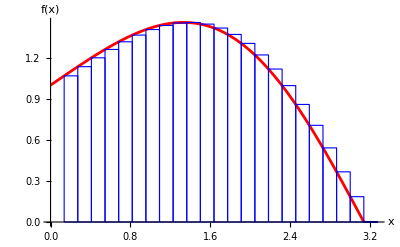

Exact integral value: 3.4366

Approximate integral value: 3.3654

{π/23,(2 π)/23,(3 π)/23,(4 π)/23,(5 π)/23,(6 π)/23,(7 π)/23,(8 π)/23,(9 π)/23,(10 π)/23,(11 π)/23,(12 π)/23,(13 π)/23,(14 π)/23,(15 π)/23,(16 π)/23,(17 π)/23,(18 π)/23,(19 π)/23,(20 π)/23,(21 π)/23,(22 π)/23,π}

```mathematica
f[x_]=Cos[x/2]E^Sin[x/2]
numIntegration[f,0,Pi,23,2]
```

### Przykład własny.

x+x^3

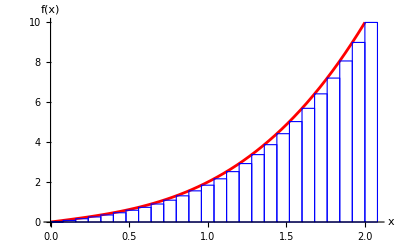

Exact integral value: 6.

Approximate integral value: 6.4064

{0,2/25,4/25,6/25,8/25,2/5,12/25,14/25,16/25,18/25,4/5,22/25,24/25,26/25,28/25,6/5,32/25,34/25,36/25,38/25,8/5,42/25,44/25,46/25,48/25,2}

```mathematica
f[x_]=x^3+x
numIntegration[f,0,2,25,1]
```